## PreLab3 Francesco Vassalli

### Q1

```mathematica
f3b[r_,c_]:=N[(2*Pi*r*c)^-1];
"Circuit 1 (Hz)="
f3b[10^4,10^-9]
f3b[r_,c_]:=N[(2*Pi*r*c)^-1];
"Circuit 2 (Hz)="
f3b[10^4,10^-9]
```

Circuit 1 (Hz)=

15915.5

Circuit 2 (Hz)=

15915.5

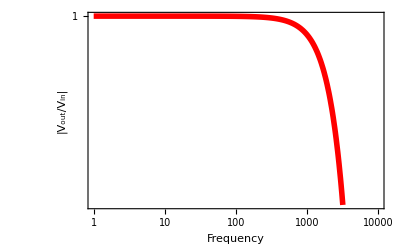

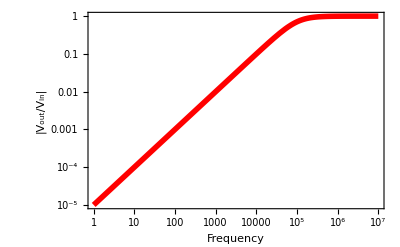

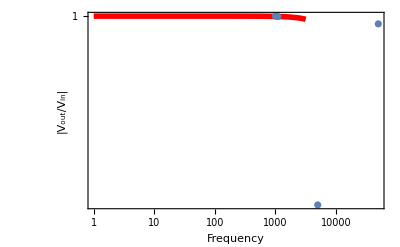

```mathematica
r=10^4;
c=10^-9;
Hhigh[ω_,res_,cap_]:=Abs[res/((ⅈ*ω*cap)^-1+res)];
Hlow[ω_,res_,cap_]:=Abs[1/(1+ⅈ*ω*cap*res)];
lowPlot=LogLogPlot[Hlow[ω,r,c],{ω,1,10000},
Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency", "|V_out/V_in|"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]}]
highPlot=LogLogPlot[Hhigh[ω,r,c],{ω,1,10000000},
Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency", "|V_out/V_in|"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]}]
fHighData= {Hhigh[1000,1000,1],Hhigh[5000,10000,.1],Hhigh[5*10^4,10000,10^-10]};
fω={1000,5000,5*10^4,1100};
fLowData={Hlow[1000,1000,10^-9],Hlow[5000,10000,5*10^-9],Hlow[5*10^4,10000,10^-10],Hlow[1100,1000,10^-8]}; 
fLowPlot=ListPlot[Thread[{fω,fLowData}],ScalingFunctions->{"Log","Log"}];
Show[lowPlot,fLowPlot,PlotRange->All]
```

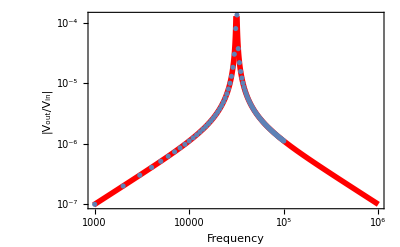

```mathematica
freq[lduct_,cap_]:=1/(2*Pi)(lduct*cap)^(-1/2);
zc[l_,c_]:=√(l/c);
q[ω_,r_,c_]:=ω*r*c;
l=10^-3;
c=10^-6;
qData={q[6000,3000,10^-9],q[12000,3000,10^-9],q[36000,3000,10^-9],q[114000,3000,10^-9],q[569000,3000,10^-9],q[3414000,3000,10^-9]};
fω={6000,12000,36000,114000,569000,3414000};
fl={8,9,10,11,12};
zData={zc[8,10^-9],zc[9,10^-9],zc[10,10^-9],zc[11,10^-9],zc[12,10^-9]};
gain[ω_]:=Abs[((ⅉ*ω*c)^-1+ⅉ*ω*l)^-1/(((ⅉ*ω*c)^-1+ⅉ*ω*l)^-1+r)];
plotgain=LogLogPlot[gain[ω],{ω,0,10^6},Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency", "|V_out/V_in|"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]}];
fgain=Table[gain[i],{i,1000,10^5,1000}];
fω=Table[i,{i,1000,10^5,1000}];
Show[plotgain,ListPlot[Thread[{fω,fgain}],ScalingFunctions->{"Log","Log"}]]
```

### Q3

The lab seems straight foward conceptually.  I like the hardest part will be substituting the coax cable and account for capacitance in the cables.  
I am not entirely sure what quality is.

### Lab Predictions

#### Circuit 1 Voltage Divider

```mathematica
r1= 9.91;
r2=6.75;
attenuation[vin_]:=r2/(r1+r2)*vin;
```

#### Low and High pass filters

9870.

16174.3

16125.1

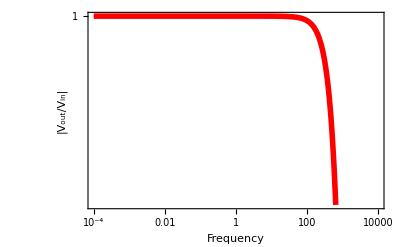

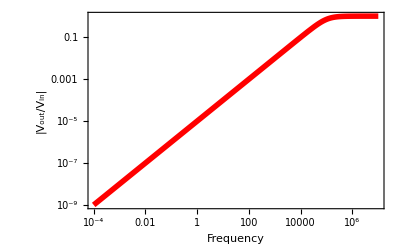

```mathematica
r3=9.84*10^3;
r4=9.87*10^3
c=10^-9;
Ghigh[ω_]:=Abs[r4/((ⅈ*ω*c)^-1+r4)];
GLow[ω_]:=Abs[1/(1+ⅈ*ω*c*r3)];
flow=(r3*c)^-1/(2*Pi)
fhigh=(r4*c)^-1/(2*Pi)
lowPlot=LogLogPlot[GLow[ω],{ω,10^-4,10000},
Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency", "|V_out/V_in|"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]}]
highPlot=LogLogPlot[Ghigh[ω],{ω,10^-4,10000000},
Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency", "|V_out/V_in|"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]}]
fHighData= {Hhigh[1000,1000,1],Hhigh[5000,10000,.1],Hhigh[5*10^4,10000,10^-10]};
fω={1000,5000,5*10^4,1100};
fLowData={Hlow[1000,1000,10^-9],Hlow[5000,10000,5*10^-9],Hlow[5*10^4,10000,10^-10],Hlow[1100,1000,10^-8]}; 
fLowPlot=ListPlot[Thread[{fω,fLowData}],ScalingFunctions->{"Log","Log"}];
```

#### Band Pass

15868.

9.84052

1003.

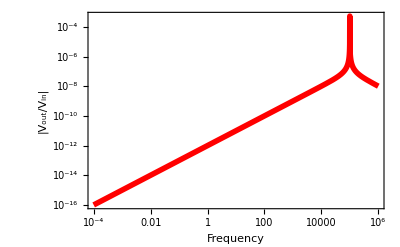

1.77397×10^-8

```mathematica
r5=9.87*10^3;
c=10^-8;
l=10.06*10^-3;
f0=(2*Pi*√(l*c))^-1
Q=f0*(2*Pi*r5*c)
Z0=√(l/c)
gain[ω_]:=Abs[((ⅉ*ω*c)^-1+ⅉ*ω*l)^-1/(((ⅉ*ω*c)^-1+ⅉ*ω*l)^-1+r5)];
plotgain=LogLogPlot[gain[ω],{ω,10^-4,10^6},Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency", "|V_out/V_in|"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]},GridLines->All]
gain[17000]
```